## SVD Unit Tests

```mathematica
SetDirectory[NotebookDirectory[]];
getTransSVD[ptsSrc_,ptsTgt_]:=Module[{cent1,cent2,matP,matQ,mat,u,w,v,r,func,vec},
(* getting the centroid *)
cent1=Mean[ptsSrc];
cent2=Mean[ptsTgt];

(* forming the cross-covariance matrix *)
matP=Map[(#-cent1)&,ptsSrc];
matQ=Map[(#-cent2)&,ptsTgt];
mat=Transpose[matP].matQ;

(* SVD decomposition *)
{u,w,v}=SingularValueDecomposition[mat];

(* obtaining the rotation *)
r=v.Transpose[u];
vec=cent2-cent1;
(* transform *)
func[pts_]:=Module[{npts,nmat,ncent},
ncent=Mean[pts];(*I think this line is a bug. I believe that this is corrected with the following line.*)
ncent=cent1;
nmat=Map[(#-ncent)&,pts];
npts=Transpose[r.Transpose[nmat]];
Map[(#+vec+ncent)&,npts]];

func];
```

```mathematica
(*Generate random points to test on in c++*)
RandomSeed[0];
randReal [e_]:=RandomReal[{-e,e}];
perturb[pts_,e_]:=Map[(Map[(#+RandomReal[{-e,e}])&,#])&,pts];
genSVDTest [n_]:=Module[{alignSource, alignTarget, mapSource, mapTest, randVec}, 
alignSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[5]]//N;
randVec = {randReal[100], randReal[100]};
(*Rotate, then translate, then add random noise*)
alignTarget = perturb[Map[(#+randVec)&,Transpose[RotationMatrix[randReal[π]].Transpose[alignSource]]], randReal[10]]//N;
mapSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[n]] //N;
 mapTest = getTransSVD[alignSource,alignTarget][mapSource]//N;
{alignSource, alignTarget, mapSource, mapTest}
]
```

```mathematica
(*Generate tests, then export them to the selected file*)
svdTests = Map[(genSVDTest[#*10])&,Range[250]]//N
(*Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\svd.json", svdTests];*)
```

{{{{30.4936,26.6141},{36.5626,13.2704},{87.0404,95.2376},{-52.3097,27.5125},{-79.7803,29.1049}},{1},{1},{{-8.50022,72.7112},{-101.464,82.3314},{-103.392,110.17},4,{-158.819,90.3021},{-158.385,91.0997},{-51.3981,83.5229}}},248,{1}}
 |  |  |  |

## Grow and Cover Unit Tests

### Utility Functions

```mathematica
ϵ=0.2;
rotM[a_]:=N[{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}];
hexM=N[rotM[π/3]];
```

```mathematica
getCoords[pt_,origin_,v1_,v2_]:=Inverse[Transpose[{v1,v2}]].(pt-origin);
getPt[coords_,origin_,v1_,v2_]:=coords.{v1,v2}+origin;
```

### Init Functions

```mathematica
getInliers[pts_,{origin_,vec_}]:=Module[{intcoords,vec2=hexM.vec,inds},
intcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,pts];
inds=Select[Range[Length[pts]],(Norm[pts⟦#⟧-getPt[intcoords⟦#⟧,origin,vec,vec2]]<ϵ*Norm[vec])&];
{inds,intcoords⟦inds⟧}];
```

```mathematica
initGridInliers[pts_,num_]:=Module[{ori,v,in={{},{}},oriTemp,vTemp,inTemp},
Do[oriTemp=RandomSample[pts,1]⟦1⟧;
vTemp=Nearest[pts,oriTemp,2]⟦2⟧-oriTemp;
inTemp=getInliers[pts,{oriTemp,vTemp}];
If[Length[inTemp⟦1⟧]>Length[in⟦1⟧],
ori=oriTemp;
v=vTemp;
in=inTemp],
{i,num}];
{{ori,v},in}];
```

```mathematica
getGrid[pts_,{inds_,intcoords_}]:=Module[{ata=Table[0,{4},{4}],atb=Table[0,{4}],a,I2=IdentityMatrix[2],res},
Do[
a=Transpose[Join[Transpose[intcoords⟦i,1⟧*I2+intcoords⟦i,2⟧*hexM],I2]];
ata+=Transpose[a].a;
atb+=Transpose[a].pts⟦inds⟦i⟧⟧,
{i,Length[inds]}

];
res=Inverse[ata].atb;

(*Origin, V1*)
{res⟦{3,4}⟧,res⟦{1,2}⟧}];
```

```mathematica
refineGrid[pts_,grid_,inliers_]:=Module[{newGrid=grid,newInliers=inliers,num=Length[inliers⟦1⟧]},
While[num<Length[pts],
(* Print["Iterate"]; *)
newGrid=getGrid[pts,newInliers];
newInliers=getInliers[pts,newGrid];
If[Length[newInliers⟦1⟧]>num,
num=Length[newInliers⟦1⟧],
Break[]]];
newGrid=getGrid[pts,newInliers];
{newGrid,newInliers}];
```

```mathematica
getGridAndCoords[pts_,num_]:=Module[{grid,inliers,v2},
{grid,inliers}=initGridInliers[pts,num];
{grid,inliers}=refineGrid[pts,grid,inliers];
v2=hexM.grid⟦2⟧;
{grid,Map[Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]]&,pts]}];
```

### Init Functions Tests (pulls from hexfit.json)

```mathematica
(*Test Function*)
getRangeRatio[pts_,r_]:=Map[{(1-r)Mean[#]+r#⟦1⟧,(1-r)Mean[#]+r#⟦2⟧}&,Transpose[{Map[Min,Transpose[pts]],Map[Max,Transpose[pts]]}]];
drawFit[pts_,{origin_,vec_},intcoords_,ptSize_]:=Module[{r=getRangeRatio[pts,1.2],rcoords,lx,hx,ly,hy,vec2=hexM.vec,inds, outinds},
inds=getInliers[pts,{origin,vec}][[1]];
outinds=Complement[Range[Length[pts]],inds];
rcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,{{r⟦1,1⟧,r⟦2,1⟧},{r⟦1,1⟧,r⟦2,2⟧},{r⟦1,2⟧,r⟦2,1⟧},{r⟦1,2⟧,r⟦2,2⟧}}];
{lx,ly}=Map[Min,Transpose[rcoords]];
{hx,hy}=Map[Max,Transpose[rcoords]];

Graphics[{
{LightGray,Table[Line[{getPt[{x,ly},origin,vec,vec2],getPt[{x,hy},origin,vec,vec2]}],{x,lx,hx}],
Table[Line[{getPt[{lx,y},origin,vec,vec2],getPt[{hx,y},origin,vec,vec2]}],{y,ly,hy}]},
(* calculated grid points *)
{Blue,AbsolutePointSize[ptSize],Map[Point[getPt[#,origin,vec,vec2]]&,intcoords]},
(* outlier points *)
{Red, AbsolutePointSize[ptSize],Map[Point,pts⟦outinds⟧]},
(* inlier points *)
{Green, AbsolutePointSize[ptSize],Map[Point,pts⟦inds⟧]},
(* grid *)
{Black, AbsolutePointSize[ptSize*2],Point[origin]},
{Black,AbsoluteThickness[ptSize],Line[{origin,origin+vec}]}

},
PlotRange->r]];
```

{{{-7.78481,0.0814371},{-0.242362,0.971632}},{{8.97719,2.01098},{0.507979,-0.661998}},{{-2.71391,16.8007},{-0.765892,-0.641409}},{{-6.89487,-5.96073},{0.561557,0.837356}},{{-13.9998,2.77034},{-0.412919,-0.907285}}}

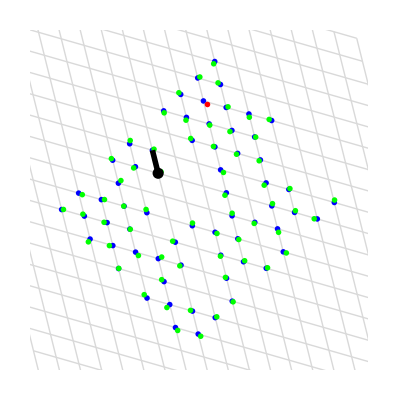
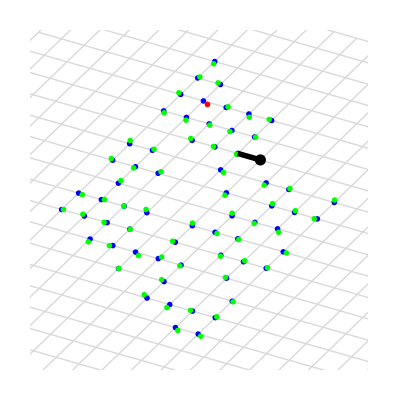
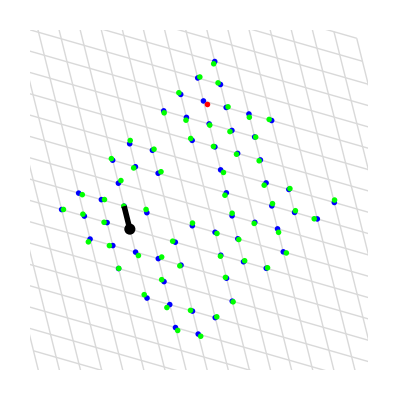
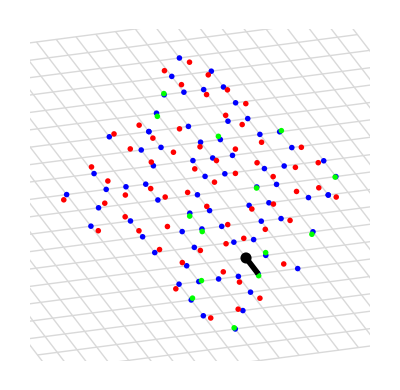
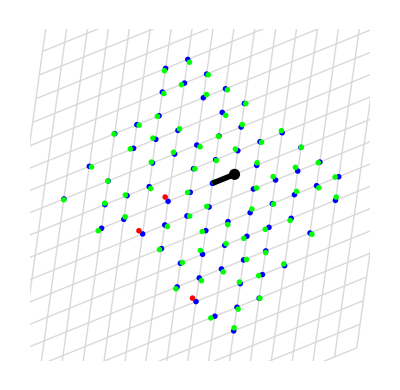
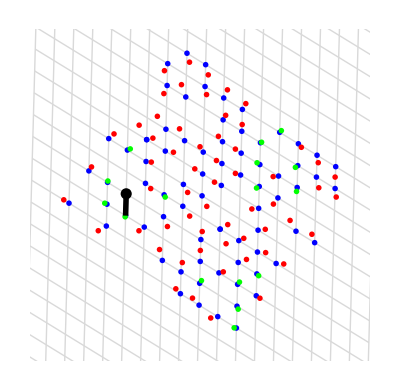
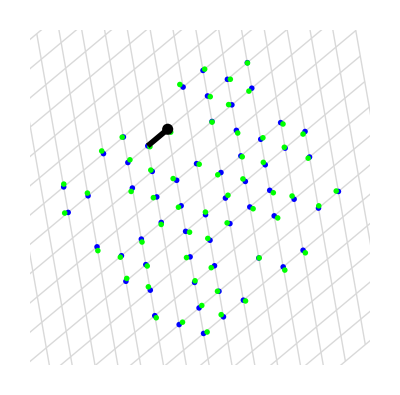
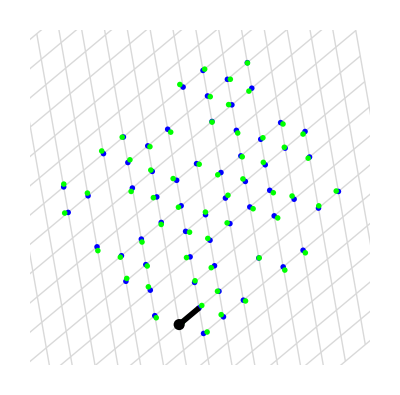
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\hexResults.json"];
importedData[[;;,2]]
importedPlots=Map[(drawFit[#[[1]],#[[2]],#[[3]],4])&,importedData];
mathematicaPlots:=Map[(drawFit[#[[1]],#[[2]][[1]],#[[2]][[2]],4])&,Map[({#[[1]],getGridAndCoords[#[[1]], 50]})&,importedData]];
Column[Transpose[{importedPlots,mathematicaPlots,mathematicaPlots}]]
```

#### RefineGrid Tests (RefineGridMathematica)

```mathematica
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\refineResults.json"];
realInitGrids = Map[(getGrid[#[[1]],getInliers[ #[[1]],#[[2]]]])&,importedData];
newGrids = Map[(refineGrid[#[[1]],#[[2]], getInliers[#[[1]],#[[2]]]][[1]])&,importedData];
MapThread[(#1 - #2[[3]])&,{realInitGrids, importedData}](*getGrid Comparison*)
MapThread[(#1 - #2[[4]])&,{newGrids, importedData}](*refineGrid Comparison*)
```

{{{-8.82914×10^-6,-3.82022×10^-6},{5.95459×10^-7,2.42472×10^-7}},{{1.05395×10^-6,3.50236×10^-7},{9.21714×10^-8,4.15258×10^-8}},{{-2.43247×10^-6,3.85323×10^-7},{1.34323×10^-6,3.62396×10^-7}},{{5.67896×10^-7,5.18815×10^-7},{6.13141×10^-8,5.33977×10^-8}},{{9.04259×10^-6,-2.11829×10^-8},{-1.90718×10^-8,2.08783×10^-6}}}

{{{-2.59173×10^-6,9.55499×10^-7},{9.5049×10^-8,-1.73983×10^-7}},{{-1.14748×10^-6,-1.0365×10^-6},{4.23283×10^-8,-1.296×10^-8}},{{-1.50345×10^-6,-0.0000103483},{-8.76385×10^-7,6.48411×10^-7}},{{-2.58238×10^-7,-5.19253×10^-7},{-1.88553×10^-8,1.96165×10^-7}},{{7.35329×10^-6,2.23876×10^-7},{3.4718×10^-7,-8.3152×10^-7}}}

### The Grow Function

```mathematica
growAndCover[pts_,samples_,wid_,num_]:=Module[{hash,ncoords={},grid,coords,loc,nghbs={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}},nghbs2,v2,bd,nbd},
(* Compute grid and coordinates *)
{grid,coords}=getGridAndCoords[pts,num];
(*Print[grid];*)
v2=hexM.grid⟦2⟧;

(* Store existing points in hash *)
hash[_,_]=False;
Scan[(hash[#⟦1⟧,#⟦2⟧]=True)&,coords];

(* for each sample, if its nearest grid point and or any of its 6-neighbors are not in the list, add them to the list *)
nghbs2=Append[nghbs,{0,0}];
Scan[
(
loc=Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]];
Scan[
If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#]
]&
,nghbs2])&
,samples];

(* growing *)
bd=Join[coords,ncoords]; (* queue of points added in the previous iteration *)
Do[
nbd={}; (* queue of points added in this iteration *)
Scan[
(loc=#;
Scan[If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#];
AppendTo[nbd,loc+#]]&,nghbs])&,
bd];
bd=nbd,
{i,wid}];

Map[getPt[#,grid⟦1⟧,grid⟦2⟧,v2]&,ncoords]];
```

```mathematica
(*Use thresholded deviation from point grid to unit text hexfit functionality*)
```

### Grow Tests

```mathematica
pts={{1,1},{2,2},{3,3}}
```

{{1,1},{2,2},{3,3}}

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts0=growAndCover[pts,samples,0,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts1=growAndCover[pts,samples,1,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts2=growAndCover[pts,samples,2,50];
```

```mathematica
graphGrow[pts_,samples_,npts0_,npts1_, npts2_]:=Module[{},
Graphics[{Map[Point,pts],{Red,Map[Point,samples]},{Yellow,Map[Point,npts2]},{Green,Map[Point,npts1]},{Blue,Map[Point,npts0]}}]
];
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\growResults.json"];
importedPlots:=Map[(graphGrow[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]])&,importedData];
mathematicaPlots:=Map[(graphGrow[
#[[1]],#[[2]],
growAndCover[#[[1]],#[[2]],0,75],
growAndCover[#[[1]],#[[2]],1,75],
growAndCover[#[[1]],#[[2]],2,75]
])&,importedData];
Column[Transpose[{importedPlots,mathematicaPlots}]];
```

## TSV Import Unit Tests

### Functions

```mathematica
getClusterArray[n_,i_]:=Module[{arr=Table[0,{n}]},arr⟦i⟧=1;arr];
numRANSAC=5;
widBuffer=2;
```

```mathematica
loadTSV[fname_,sliceNames_,sliceInd_,tissueInd_,rowcolInds_,clusterInd_,featureInds_,zDis_,srctgts_]:=Module[{slices,vals,clusters,tab,records,nclusters,nfeatures,nm,xyInds=Reverse[rowcolInds],names,nslices},
tab=Import[fname];
names=Append[tab⟦1,featureInds⟧,"No tissue"];
tab=Drop[tab,1];

nclusters = Max[Select[tab⟦;;,clusterInd⟧,NumberQ]]+1;
nfeatures=Length[featureInds];
records=Map[(nm=#;Select[tab,(#⟦sliceInd⟧==nm&&#⟦tissueInd⟧==1)&])&,sliceNames];
slices=Table[
If[i==1,
records⟦i,;;,xyInds⟧,
getTransSVD[srctgts⟦i-1,1⟧,srctgts⟦i-1,2⟧][records⟦i,;;,xyInds⟧]],
{i,Length[sliceNames]}];
clusters=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nclusters+1,nclusters+1],
getClusterArray[nclusters+1,#⟦clusterInd⟧+1]]&,#]&,records];
vals=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nfeatures+1,nfeatures+1],
Append[#⟦featureInds⟧,0]]&,#]&,records];

(* Add buffer to each slice and cover neighboring slices *)
nslices=Table[
Switch[i,
1,
growAndCover[slices⟦i⟧,slices⟦i+1⟧,widBuffer,numRANSAC],
Length[slices],
growAndCover[slices⟦i⟧,slices⟦i-1⟧,widBuffer,numRANSAC],
_,
growAndCover[slices⟦i⟧,Join[slices⟦i-1⟧,slices⟦i+1⟧],widBuffer,numRANSAC]],{i,Length[slices]}];

slices=Table[Map[Append[#,i*zDis]&,Join[slices⟦i⟧,nslices⟦i⟧]],{i,Length[slices]}];
clusters=MapThread[Join[#1,Map[getClusterArray[nclusters+1,nclusters+1]&,#2]]&,{clusters,nslices}];
vals=MapThread[Join[#1,Map[getClusterArray[nfeatures+1,nfeatures+1]&,#2]]&,{vals,nslices}];

(* add empty top and bottom slices *)
slices=Prepend[Append[slices,Map[(#+{0,0,zDis})&,Last[slices]]],Map[(#+{0,0,-zDis})&,First[slices]]];
clusters=
Prepend[Append[clusters,
Map[getClusterArray[nclusters+1,nclusters+1]&,Last[slices]]],
Map[getClusterArray[nclusters+1,nclusters+1]&,First[slices]]];
vals=
Prepend[Append[vals,
Map[getClusterArray[nfeatures+1,nfeatures+1]&,Last[slices]]],
Map[getClusterArray[nfeatures+1,nfeatures+1]&,First[slices]]];

{slices,clusters,vals,names}
]
```

## 2D Contour Tests

#### 2D Contour Implementation

```mathematica
orientation[u_,v_]:=Sign[Cross[Append[u,0],Append[v,0]]⟦3⟧];
```

```mathematica
getMaxPos[vals_]:=MaximalBy[Range[Length[vals]],vals⟦#⟧&]⟦1⟧;
```

```mathematica
getMassPoint[pts_]:=Mean[Select[pts,#≠{}&]];
```

```mathematica
interpEdge2Mat[p_,q_,pvals_,qvals_]:=Module[
{t=Abs[pvals⟦1⟧-pvals⟦2⟧]/(Abs[pvals⟦1⟧-pvals⟦2⟧]+Abs[qvals⟦1⟧-qvals⟦2⟧])},
(1-t)p+t*q
];
```

```mathematica
contourTriMultiDC[pts_,tris_,vals_]:=Module[{ptMats,nmat=Length[vals⟦1⟧],verts,segs,segMats,edgeHash,edges,edgeFaces,edgePtInds,npts=Length[pts],ntris=Length[tris],edgeMap={{1,2},{2,3},{3,1}},ind,edgePoints,triVertInds,newseg,ct,ct2,ct3,bdVertInd,fillVerts,fillTris,fillMats,seg},
(* get material index at each point *)
ptMats=Map[getMaxPos,vals];

(* create adj table from edges to faces *)
edgeHash[_,_]=0;
edges=Table[{},{ntris*3}];
edgeFaces=Table[{},{ntris*3}];
ct=0;
Do[If[(ind=edgeHash[
tris⟦i,edgeMap⟦j,1⟧⟧,
tris⟦i,edgeMap⟦j,2⟧⟧
])==0,
ct+=1;
edges⟦ct⟧=tris⟦i,edgeMap⟦j⟧⟧;
edgeFaces⟦ct⟧={i};
edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧]=ct;
edgeHash[tris⟦i,edgeMap⟦j,2⟧⟧,tris⟦i,edgeMap⟦j,1⟧⟧]=ct,
AppendTo[edgeFaces⟦ind⟧,i]],
{i,ntris},{j,3}];
edges=edges⟦1;;ct⟧;
edgeFaces=edgeFaces⟦1;;ct⟧;
(* create interpolation points, one per edge with material change *)
edgePoints=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧,
{},
interpEdge2Mat[pts⟦#⟦1⟧⟧,pts⟦#⟦2⟧⟧,vals⟦#⟦1⟧,ptMats⟦#⟧⟧,vals⟦#⟦2⟧,ptMats⟦#⟧⟧]]&,edges];
edgePtInds=Table[0,{Length[edges]}];

(* create vertices, one per triangle with material change *)
verts=Table[{},{ntris*7}];
ct=0;
triVertInds=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧==ptMats⟦#⟦3⟧⟧,
0,
ind=#;
ct+=1;
verts⟦ct⟧=getMassPoint[edgePoints⟦
Map[edgeHash[ind⟦#⟦1⟧⟧,ind⟦#⟦2⟧⟧]&,edgeMap]
⟧];
ct]&,
tris];

(* create segments *)
segs=Table[{},{Length[edges]}];
segMats=Table[{},{Length[edges]}];
ct2=0;
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
ct2+=1;
segMats⟦ct2⟧=ptMats⟦edges⟦i⟧⟧;
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
ct+=1;
verts⟦ct⟧=edgePoints⟦i⟧;
edgePtInds⟦i⟧=ct;
newseg={triVertInds⟦edgeFaces⟦i,1⟧⟧,ct},
(* interior edge: connect two triangle points *)
newseg=triVertInds⟦edgeFaces⟦i⟧⟧];
If[orientation[pts⟦edges⟦i,1⟧⟧-pts⟦edges⟦i,2⟧⟧,verts⟦newseg⟦1⟧⟧-pts⟦edges⟦i,1⟧⟧]<0,
newseg=Reverse[newseg]];
segs⟦ct2⟧=newseg],
{i,Length[edges]}];

verts=verts⟦1;;ct⟧;
segs=segs⟦1;;ct2⟧;
segMats=segMats⟦1;;ct2⟧;

(* create fill triangles *)
fillVerts=Join[verts,pts];
fillTris=Table[{},{ntris*6}];
fillMats=Table[0,{ntris*6}];
ct3=0;

(* first type of triangles: dual to mesh edges with a material change *)
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
seg={triVertInds⟦edgeFaces⟦i,1⟧⟧,edgePtInds⟦i⟧},
(* interior edge: connect two triangle points *)
seg=triVertInds⟦edgeFaces⟦i⟧⟧];
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,1⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,1⟧⟧;
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,2⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,2⟧⟧
],
{i,Length[edges]}
];

(* second type of triangles: original mesh triangle, if there is no material change, or a third of the triangle, if there is some edge with no material change *)
Do[
If[ptMats⟦tris⟦i,1⟧⟧==ptMats⟦tris⟦i,2⟧⟧==ptMats⟦tris⟦i,3⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=tris⟦i⟧+{ct,ct,ct};
fillMats⟦ct3⟧=ptMats⟦tris⟦i,1⟧⟧,
Do[If[ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧==ptMats⟦tris⟦i,edgeMap⟦j,2⟧⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=Append[tris⟦i,edgeMap⟦j⟧⟧+{ct,ct},triVertInds⟦i⟧];
fillMats⟦ct3⟧=ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧],
{j,3}]
],
{i,Length[tris]}];

(* Print[ct3,fillVerts,fillTris,fillMats]; *)
fillTris=fillTris⟦1;;ct3⟧;
fillMats=fillMats⟦1;;ct3⟧;

{verts,segs,segMats,fillVerts,fillTris,fillMats}
];
```

```mathematica
perp[{x_,y_}]:={-y,x}
```

```mathematica
getContourByMat2D[verts_,segs_,segmats_,mat_,shrink_]:=Module[{inds1,inds2,nsegs,nvertInds,nverts,vertUsed,vertNewInds,vertnorms,nm},
(* select segments by mat *)
inds1=Select[Range[Length[segs]],segmats⟦#,1⟧==mat&];
inds2=Select[Range[Length[segs]],segmats⟦#,2⟧==mat&];
nsegs=Join[segs⟦inds1⟧,Map[Reverse,segs⟦inds2⟧]];
(* prune unused vertices *)
vertUsed=Map[False&,verts];
Scan[(vertUsed⟦#⟦1⟧⟧=True;vertUsed⟦#⟦2⟧⟧=True)&,nsegs];
nvertInds=Pick[Range[Length[verts]],vertUsed];
vertNewInds=Map[0&,verts];
Do[vertNewInds⟦nvertInds⟦i⟧⟧=i,{i,Length[nvertInds]}];
nverts=verts⟦nvertInds⟧;
nsegs=Map[vertNewInds⟦#⟧&,nsegs,{2}];
(* shrink *)
vertnorms=Map[{0,0}&,nverts];
Scan[(nm=perp[nverts⟦#⟦2⟧⟧-nverts⟦#⟦1⟧⟧];
vertnorms⟦#⟦1⟧⟧+=nm;
vertnorms⟦#⟦2⟧⟧+=nm)&,nsegs];
nverts+=shrink*Map[Normalize,vertnorms];
{nverts,nsegs}];
```

```mathematica
getContourAllMats2D[verts_,segs_,segmats_,nmat_,shrink_]:=Table[getContourByMat2D[verts,segs,segmats,i,shrink],{i,nmat}];
```

```mathematica
getSectionContours[pts_,vals_,shrink_]:=Module[{tris,npts,z=pts⟦1,3⟧,reg,verts,segs,segmats,fverts,ftris,fmats, nmat=Length[vals⟦1⟧],ctrs},
npts=Map[#⟦{1,2}⟧&,pts];
reg=DelaunayMesh[npts];
tris=Map[First,MeshCells[reg,2]];
{verts,segs,segmats,fverts,ftris,fmats}=contourTriMultiDC[npts,tris,vals];
ctrs=getContourAllMats2D[verts,segs,segmats,nmat,shrink];
{
Map[{
Map[
Append[#,z]&,#⟦1⟧
],#⟦2⟧
}&,ctrs],
{
Map[Append[#,z]&,fverts],ftris,fmats
}
}
];
```

```mathematica
getSectionContoursAll[sections_,vals_,shrink_]:=Transpose[MapThread[getSectionContours[#1,#2,shrink]&,{sections,vals}]];
```

#### Tests

```mathematica
(*Delauney Test*)
elements=Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\triangleResults.json"];
genMesh[pts_,tris_]:= MeshRegion[pts,Map[Triangle,tris],PlotTheme->"Lines", BaseStyle->{Black,EdgeForm[Dashed]}];
compareDelauney[pts_,tris_]:=
Overlay[{genMesh[pts,tris],DelaunayMesh[pts, PlotTheme->"Lines",BaseStyle->{LightGray,Thin,EdgeForm[Dashed]}]}];
Map[compareDelauney[#[[1]], Map[#+1&,#[[2]]]]&, elements];
(*ensure the same number of faces with the same number of vertices are found. Should be all true*)
Map[Dimensions[Map[#+1&,#[[2]]]]== Dimensions[Map[First,MeshCells[DelaunayMesh[#[[1]]],2]]]&,elements];
```

```mathematica
(*Single-layer Contour Test*)
(*Generate Single Triangle example*)
n=9;nMat=2;ptsize=0.02;
SeedRandom[0];
pts={{0,0},{1,0},{0,1}}//N;
vals={{1,0},{1,0},{1,0}};
mesh=DelaunayMesh[pts];
tris=Map[First,MeshCells[mesh,2]];
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourTest.json", {pts, vals,tris}];
```

```mathematica
(*Single-layer Contour Test*)
(*Generate Two Triangle (2 mats) example*)
n=9;nMat=2;ptsize=0.02;
SeedRandom[0];
pts={{-1,0},{1,0},{0,1}, {0,-1}}//N;
vals={{0,1},{1,0},{1,0},{1,0}}//N;
mesh=DelaunayMesh[pts];
tris=Map[First,MeshCells[mesh,2]];
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourTest.json", {pts, vals,tris}];
```

```mathematica
(*Single-layer Contour Test*)
(*Generate Two Triangle (3 mats) example*)
n=9;nMat=2;ptsize=0.02;
SeedRandom[0];
pts={{-1,0},{1,0},{0,1}, {0,-1}}//N;
vals={{0,1},{0,1},{1,0},{1,0}}//N;
mesh=DelaunayMesh[pts];
tris=Map[First,MeshCells[mesh,2]];
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourTest.json", {pts, vals,tris}];
```

```mathematica
(*Single-layer Contour Test*)
(*Generate circle example*)
n=9;nMat=2;ptsize=0.02;
SeedRandom[0];
pts={{0,0},{1/Sqrt[2],1/Sqrt[2]},{-1/Sqrt[2],1/Sqrt[2]},{-1/Sqrt[2],-1/Sqrt[2]},{1/Sqrt[2],-1/Sqrt[2]},{1,0},{0,1},{-1,0},{0,-1}}//N;
vals={{0,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}};
mesh=DelaunayMesh[pts];
tris=Map[First,MeshCells[mesh,2]];
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourTest.json", {pts, vals,tris}];
```

```mathematica
(*Single-layer Contour Test*)
(*Generate random layer*)
n=100;nMat=4;ptsize=0.02;
SeedRandom[0];
pts=RandomReal[{-1,1},{n,2}];
vals=RandomReal[{0,1},{n,nMat}];
mesh=DelaunayMesh[pts];
tris=Map[First,MeshCells[mesh,2]];
Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourTest.json", {pts, vals,tris}];
```

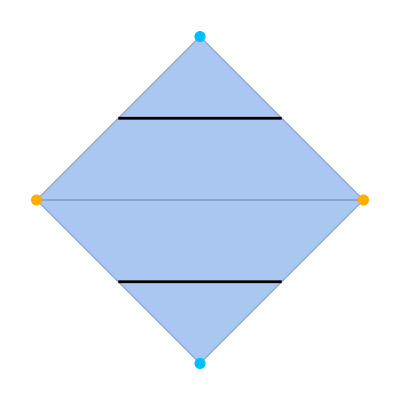
{-Graphics-,-Graphics-}

```mathematica
(*Display Mathematica result*)
{verts,segs,segmats,fverts,ftris,fmats}=contourTriMultiDC[pts,tris,vals];

{nverts,nsegs,nsegmats}=contourTriMultiDCRefined[pts,tris,vals];
Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[nverts,nsegs,ptsize/2,False]
];
(*C++ Result*)
{verts2,segs2} = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\singleContourResults.json"];
Dimensions[verts2];
{Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,ptsize/2,False]
],
Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts2,Map[#+1&,segs2],ptsize/2,False]
]}
```